## Stratified Photon Mapping:

Constant kernel:

```mathematica
(* 2D case*)
```

```mathematica
∫_(√(k - 1))^(√k) IP* 2 * Subscript[r, k] ⅆ Subscript[r, k]
```

2 IP ((1-k)/2+k/2)

```mathematica
Simplify[2 IP ((1-k)/2+k/2)]
```

IP

```mathematica
∫_(√(k - 1))^(√k) (k * IP)/Subscript[r, k]^2* 2 * Subscript[r, k] ⅆ Subscript[r, k] (*radius √n*)
```

ConditionalExpression[IP k (-Log[-1+k]+Log[k]), ]

```mathematica
∫_((√(k - 1))/(√n))^((√k)/(√n)) (k * IP)/(Subscript[r, k]^2*n)* 2 * Subscript[r, k]* nⅆ Subscript[r, k]  (*radius 1*)
```

ConditionalExpression[IP k (-Log[-1+k]+Log[k]), ]

```mathematica
(*3D case*)
```

```mathematica
∫_((k - 1)^(1/3))^(k^(1/3)) (k * DP)/Subscript[r, k]^3* 3 * Subscript[r, k]^2 ⅆ Subscript[r, k] (*radius √n*)
```

ConditionalExpression[DP k (-Log[-1+k]+Log[k]), ]

```mathematica
∫_((k - 1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) (k * DP)/(Subscript[r, k]^3*n)* 3 * Subscript[r, k]^2* nⅆ Subscript[r, k]  (*radius 1*)
```

ConditionalExpression[DP k (-Log[-1+k]+Log[k]), ]

Epanechnikov kernel:

```mathematica
(*Definition of the Epanechnikov kernel for Photon Mapping*)
```

```mathematica
Subscript[K, Subscript[r, k]][r_]:= 2/(π*Subscript[r, k]^2)* (1 - (Subscript[r, i] * (1/Subscript[r, k]))^2)
```

```mathematica
(*Inner integral 2D case*)
```

```mathematica
∫_((√(i-1))/(√n))^((√i)/(√n)) 2/(π*Subscript[r, k]^2)* (1 - (Subscript[r, i]/Subscript[r, k])^2)* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k] * n^2 ⅆ Subscript[r, i]
```

(2 ϕ)/(π r_k^3)-(4 i ϕ)/(π r_k^3)+(4 n ϕ)/(π r_k)

```mathematica
Simplify[(2 ϕ)/(π Subscript[r, k]^3)-(4 i ϕ)/(π Subscript[r, k]^3)+(4 n ϕ)/(π Subscript[r, k])]
```

(2 ϕ (1-2 i+2 n r_k^2))/(π r_k^3)

```mathematica
(*Outer integral 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) (2 ϕ (1-2 i+2 n Subscript[r, k]^2))/(π Subscript[r, k]^3)ⅆ Subscript[r, k]
```

ConditionalExpression[(n ϕ (1-2 i-2 (-1+k) k (Log[-1+k]-Log[k])))/((-1+k) k π), ]

```mathematica
(*Sum up to the (k-1)th Photon*)
```

```mathematica
∑_(i=1)^(k-1) (n ϕ (1-2 i-2 (-1+k) k (Log[-1+k]-Log[k])))/((-1+k) k π)  (*result with sum method*)
```

```mathematica
-((-1+k) n ϕ (1+2 k Log[-1+k]-2 k Log[k]))/(k π)
```

```mathematica
(*Inner integral over the whole interval 2D case*)
```

```mathematica
∫_0^((√(k-1))/(√n)) 2/(π*Subscript[r, k]^2)* (1 - (Subscript[r, i]/Subscript[r, k])^2)* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k] * n^2 ⅆ Subscript[r, i]
```

-(2 (-1+k) ϕ (-1+k-2 n r_k^2))/(π r_k^3)

```mathematica
(*Outer integral based on the whole interval 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) -(2 (-1+k) ϕ (-1+k-2 n Subscript[r, k]^2))/(π Subscript[r, k]^3)ⅆ Subscript[r, k]  (*result with integral method*)
```

ConditionalExpression[-((-1+k) ϕ (n+4 k n Log[(√(-1+k))/(√n)]-4 k n Log[(√k)/(√n)]))/(k π), ]

```mathematica
(*3D*)
```

```mathematica
(*Inner Integral 3D case*)
```

```mathematica
∫_0^((k-1)^(1/3)/n^(1/3)) 15/(8*π*Subscript[r, k]^3)* (1 - (Subscript[r, i]/Subscript[r, k])^2)* ϕ* 3 * Subscript[r, i]^2 * 3 * Subscript[r, k]^2 * n^2 ⅆ Subscript[r, i]
```

(9 (-1+k) n^(1/3) ϕ (-3 (-1+k)^(2/3)+5 n^(2/3) r_k^2))/(8 π r_k^3)

```mathematica
(*Outer integral 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) ((9 (-1+k) n^(1/3) ϕ (-3 (-1+k)^(2/3)+5 n^(2/3) Subscript[r, k]^2))/(8 π Subscript[r, k]^3))ⅆ Subscript[r, k]
```

ConditionalExpression[(3 (-1+k) n ϕ (9 (-1+k)^(2/3)+k^(2/3) (-9-10 Log[-1+k]+10 Log[k])))/(16 k^(2/3) π), ]

```mathematica
(*Inner integral for the normalization costant 2D case*)
```

```mathematica
∫_0^Subscript[r, k] (1-(Subscript[r, i]/Subscript[r, k])^2)Subscript[r, i] ⅆ Subscript[r, i]
```

r_k^2/4

```mathematica
(*Outer integral for the normalization constant 2D case*)
```

```mathematica
∫_0^(2π) (Subscript[r, k]^2/4)ⅆθ
```

```mathematica
(π Subscript[r, k]^2)/2     (*2D Normalization*)
```

```mathematica
(*Inner integral for the normalization constant 3D case*)
```

```mathematica
∫_0^Subscript[r, k] (1-(Subscript[r, i]/Subscript[r, k])^2)Subscript[r, i]^2* Sin[ϕ] ⅆ Subscript[r, i]
```

2/15 Sin[ϕ] r_k^3

```mathematica
(*Second inner integral for the normalization constant 3D case*)
```

```mathematica
∫_0^π (2/15 Sin[ϕ] Subscript[r, k]^3)ⅆϕ
```

(4 r_k^3)/15

```mathematica
(*Outer integral for the nomalization constant 3D case*)
```

```mathematica
∫_0^(2π) ((4 Subscript[r, k]^3)/15)ⅆθ
```

```mathematica
(8 π Subscript[r, k]^3)/15    (*3D Normalization*)
```

Cone filter:

```mathematica
(*Definition of the Cone filter for Photon Mapping*)
```

```mathematica
Subscript[K, Subscript[r, k]][d_]:= (1 - d/(s * Subscript[r, k]))/(π * Subscript[r, k]^2 * (1 - 2/(3 * s)))
```

```mathematica
(*Inner integral 2D case*)
```

```mathematica
∫_0^((√(k-1))/(√n)) (1 - Subscript[r, i]/(s * Subscript[r, k]))/(π * Subscript[r, k]^2 * (1 - 2/(3 * s)))* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k] * n^2 ⅆ Subscript[r, i]
```

(2 (-1+k) √n ϕ (-2 √(-1+k)+3 √n s r_k))/(π (-2+3 s) r_k^2)

```mathematica
FullSimplify[(2 (-1+k) √n ϕ (-2 √(-1+k)+3 √n s Subscript[r, k]))/(π (-2+3 s) Subscript[r, k]^2)]
```

(2 (-1+k) √n ϕ (-2 √(-1+k)+3 √n s r_k))/(π (-2+3 s) r_k^2)

```mathematica
(*Outer integral 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) (2 (-1+k) √n ϕ (-2 √(-1+k)+3 √n s Subscript[r, k]))/(π (-2+3 s) Subscript[r, k]^2)ⅆ Subscript[r, k]    (*result with integral method*)
```

ConditionalExpression[((-1+k) n ϕ (-4+4 √((-1+k)/k)-3 s Log[-1+k]+3 s Log[k]))/(π (-2+3 s)), ]

```mathematica
(*Integral for the k th photon 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) (1 - Subscript[r, k]/(s * Subscript[r, k]))/(π * Subscript[r, k]^2 * (1 - 2/(3 * s)))* ϕ * 2 * Subscript[r, k] * nⅆ Subscript[r, k]
```

ConditionalExpression[(6 n (-1+s) ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π (-2+3 s)), ]

```mathematica
(*Sum of the result of the photons up to the (k-1) th  and the result of the k th photon*)
```

```mathematica
(6 n (-1+s) ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π (-2+3 s))+ ((-1+k) n ϕ (-4+4 √((-1+k)/k)-3 s Log[-1+k]+3 s Log[k]))/(π (-2+3 s))
```

((-1+k) n ϕ (-4+4 √((-1+k)/k)-3 s Log[-1+k]+3 s Log[k]))/(π (-2+3 s))+(6 n (-1+s) ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π (-2+3 s))

```mathematica
FullSimplify[((-1+k) n ϕ (-4+4 √((-1+k)/k)-3 s Log[-1+k]+3 s Log[k]))/(π (-2+3 s))+(6 n (-1+s) ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π (-2+3 s))]
```

(n ϕ ((4 (√(-1+k)-√k) (-1+k))/(√k)+(3-3 k s) Log[-1+k]+3 (-1+k s) Log[k]))/(π (-2+3 s))

```mathematica
(*Inner integral 3D case*)
```

```mathematica
∫_0^((k-1)^(1/3)/n^(1/3)) (1 - Subscript[r, i]/(s * Subscript[r, k]))/((π (-3+4 s) Subscript[r, k]^3)/(3 s))* ϕ* 3 * Subscript[r, i]^2 * 3 * Subscript[r, k]^2 * n^2 ⅆ Subscript[r, i]  (* 3D Case *)
```

(9 (-1+k) n^(2/3) ϕ (-3 (-1+k)^(1/3)+4 n^(1/3) s r_k))/(4 π (-3+4 s) r_k^2)

```mathematica
(*Outer integral 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) ((9 (-1+k) n^(2/3) ϕ (-3 (-1+k)^(1/3)+4 n^(1/3) s Subscript[r, k]))/(4 π (-3+4 s) Subscript[r, k]^2))ⅆ Subscript[r, k]
```

ConditionalExpression[(3 (-1+k) n ϕ (-9+9 ((-1+k)/k)^(1/3)-4 s Log[-1+k]+4 s Log[k]))/(4 π (-3+4 s)), ]

```mathematica
(*Integral for the k th photon 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) (1 - 1/s)/((π (-3+4 s) Subscript[r, k]^3)/(3 s))* ϕ * 3 * Subscript[r, k]^2 * nⅆ Subscript[r, k]
```

ConditionalExpression[(3 n (-1+s) ϕ (-Log[-1+k]+Log[k]))/(π (-3+4 s)), ]

```mathematica
(*Sum of the result of the photons up to the (k-1)th and the k th photon*)
```

```mathematica
(3 (-1+k) n ϕ (-9+9 ((-1+k)/k)^(1/3)-4 s Log[-1+k]+4 s Log[k]))/(4 π (-3+4 s)) + (3 n (-1+s) ϕ (-Log[-1+k]+Log[k]))/(π (-3+4 s))
```

(3 n (-1+s) ϕ (-Log[-1+k]+Log[k]))/(π (-3+4 s))+(3 (-1+k) n ϕ (-9+9 ((-1+k)/k)^(1/3)-4 s Log[-1+k]+4 s Log[k]))/(4 π (-3+4 s))

```mathematica
FullSimplify[(3 n (-1+s) ϕ (-Log[-1+k]+Log[k]))/(π (-3+4 s))+(3 (-1+k) n ϕ (-9+9 ((-1+k)/k)^(1/3)-4 s Log[-1+k]+4 s Log[k]))/(4 π (-3+4 s))]
```

1/(4 π (-3+4 s))3 n ϕ (9 (-1+((-1+k)/k)^(1/3)) (-1+k)+(4-4 k s) Log[-1+k]+4 (-1+k s) Log[k])

```mathematica
(*Inner integral for the normalization constant 2D case*)
```

```mathematica
∫_0^Subscript[r, k] (1 - Subscript[r, i]/(s * Subscript[r, k]))Subscript[r, i] ⅆ Subscript[r, i]
```

r_k^2/2-r_k^2/(3 s)

```mathematica
(*Outer integral for the normalization constant 2D case*)
```

```mathematica
∫_0^(2π) (Subscript[r, k]^2/2-Subscript[r, k]^2/(3 s))ⅆθ
```

```mathematica
2 π (Subscript[r, k]^2/2-Subscript[r, k]^2/(3 s)) (* 2D Normalization *)
```

```mathematica
(*Inner integral for the normalization constant 3D case*)
```

```mathematica
∫_0^Subscript[r, k] (1 - Subscript[r, i]/(s * Subscript[r, k]))Subscript[r, i]^2* Sin[ϕ]ⅆ Subscript[r, i]
```

1/3 Sin[ϕ] r_k^3-(Sin[ϕ] r_k^3)/(4 s)

```mathematica
(*Sencond inner integral for  the normalization constant 3D case*)
```

```mathematica
∫_0^π (1/3 Sin[ϕ] Subscript[r, k]^3-(Sin[ϕ] Subscript[r, k]^3)/(4 s))ⅆϕ
```

((-3+4 s) r_k^3)/(6 s)

```mathematica
(*Outer integral for the normalization constant 3D case*)
```

```mathematica
∫_0^(2π) (((-3+4 s) Subscript[r, k]^3)/(6 s))ⅆθ
```

```mathematica
(π (-3+4 s) Subscript[r, k]^3)/(3 s)  (* 3D Normalization *)
```

Silverman kernel:

```mathematica
(*Definition of the Silverman kernel for Photon Mapping*)
```

```mathematica
Subscript[K, Subscript[r, k]][d_]:= 3/(π * Subscript[r, k]^2) * (1 -( d/Subscript[r, k])^2)^2
```

```mathematica
(*Inner integral 2D case*)
```

```mathematica
∫_((√(i-1))/(√n))^((√i)/(√n)) 3/(π * Subscript[r, k]^2) * (1 -( Subscript[r, i]/Subscript[r, k])^2)^2* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k]* n^2 ⅆ Subscript[r, i]
```

(2 ϕ)/(n π r_k^5)-(6 i ϕ)/(n π r_k^5)+(6 i^2 ϕ)/(n π r_k^5)+(6 ϕ)/(π r_k^3)-(12 i ϕ)/(π r_k^3)+(6 n ϕ)/(π r_k)

```mathematica
FullSimplify[(2 ϕ)/(n π Subscript[r, k]^5)-(6 i ϕ)/(n π Subscript[r, k]^5)+(6 i^2 ϕ)/(n π Subscript[r, k]^5)+(6 ϕ)/(π Subscript[r, k]^3)-(12 i ϕ)/(π Subscript[r, k]^3)+(6 n ϕ)/(π Subscript[r, k])]
```

(2 ϕ (1+3 (-1+i) i+3 n r_k^2 (1-2 i+n r_k^2)))/(n π r_k^5)

```mathematica
(*Outer integral 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) (2 ϕ (1+3 (-1+i) i+3 n Subscript[r, k]^2 (1-2 i+n Subscript[r, k]^2)))/(n π Subscript[r, k]^5)ⅆ Subscript[r, k]
```

ConditionalExpression[1/(2 (-1+k)^2 k^2 π)n ϕ (-1-3 (-1+i) i-4 k+6 i (1+i) k+6 (1-2 i) k^2-6 (-1+k)^2 k^2 (Log[-1+k]-Log[k])), ]

```mathematica
(*Sum up to the (k-1)th photon*)
```

```mathematica
∑_(i=1)^(k-1) 1/(2 (-1+k)^2 k^2 π)n ϕ (-1-3 (-1+i) i-4 k+6 i (1+i) k+6 (1-2 i) k^2-6 (-1+k)^2 k^2 (Log[-1+k]-Log[k]))
```

```mathematica
-((-1+k) n ϕ (1+4 k+6 k^2 Log[-1+k]-6 k^2 Log[k]))/(2 k^2 π) (*reuslt with the sum method*)
```

```mathematica
(*Inner integral for the whole interval 2D case*)
```

```mathematica
∫_0^((√(k-1))/(√n)) 3/(π * Subscript[r, k]^2) * (1 -( Subscript[r, i]/Subscript[r, k])^2)^2* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k]* n^2 ⅆ Subscript[r, i]
```

(2 (-1+k) ϕ ((-1+k)^2-3 (-1+k) n r_k^2+3 n^2 r_k^4))/(n π r_k^5)

```mathematica
(*Outer integral based on the whole interval 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) (2 (-1+k) ϕ ((-1+k)^2-3 (-1+k) n Subscript[r, k]^2+3 n^2 Subscript[r, k]^4))/(n π Subscript[r, k]^5)ⅆ Subscript[r, k] (*result with integral method*)
```

ConditionalExpression[((-1+k) ϕ (-n^2-4 k n^2-12 k^2 n^2 Log[(√(-1+k))/(√n)]+12 k^2 n^2 Log[(√k)/(√n)]))/(2 k^2 n π), ]

```mathematica
(*Inner integral 3D case*)
```

```mathematica
∫_0^((k-1)^(1/3)/n^(1/3)) 105/(32  Subscript[r, k]^3) * (1 -( Subscript[r, i]/Subscript[r, k])^2)^2* ϕ* 3 * Subscript[r, i]^2 * 3 * Subscript[r, k]^2 * n^2 ⅆ Subscript[r, i]    (*3D Case*)
```

(9 (-1+k) ϕ (15 (-1+k)^(4/3)-42 (-1+k)^(2/3) n^(2/3) r_k^2+35 n^(4/3) r_k^4))/(32 n^(1/3) r_k^5)

```mathematica
(*Outer integral 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) ((9 (-1+k) ϕ (15 (-1+k)^(4/3)-42 (-1+k)^(2/3) n^(2/3) Subscript[r, k]^2+35 n^(4/3) Subscript[r, k]^4))/(32 n^(1/3) Subscript[r, k]^5))ⅆ Subscript[r, k]
```

ConditionalExpression[1/(32 n^(1/3))9 (-1+k) ϕ (-1/4 n^(4/3) (69+140 Log[(-1+k)^(1/3)/n^(1/3)])+1/4 n^(4/3) ((3 (5+28 (-1+k)^(1/3) k^(2/3)-5 k) (-1+k)^(1/3))/k^(4/3)+140 Log[k^(1/3)/n^(1/3)])), ]

```mathematica
(*Inner integral for the normalization constant 2D case*)
```

```mathematica
∫_0^Subscript[r, k] ((1-(Subscript[r, i]/Subscript[r, k])^2)^2*Subscript[r, i])ⅆ Subscript[r, i]
```

r_k^2/6

```mathematica
(*Outer integral for the normalization constant 2D case*)
```

```mathematica
∫_0^(2π) Subscript[r, k]^2/6 ⅆθ
```

```mathematica
(π Subscript[r, k]^2)/3   (*2D Normalization*)
```

```mathematica
(*Inner integral for the normalization cosntant 3D case*)
```

```mathematica
∫_0^Subscript[r, k] ((1-(Subscript[r, i]/Subscript[r, k])^2)^2*Subscript[r, i]^2* Sin[ϕ])ⅆ Subscript[r, i]
```

8/105 Sin[ϕ] r_k^3

```mathematica
(*Second inner integral for  the normalization constant 3D case*)
```

```mathematica
∫_0^π 8/105 Sin[ϕ] Subscript[r, k]^3 ⅆϕ
```

(16 r_k^3)/105

```mathematica
(*Outer integral for  the normalization constant 3D case*)
```

```mathematica
∫_0^(2π) (16 Subscript[r, k]^3)/105 ⅆθ
```

```mathematica
(32 π Subscript[r, k]^3)/105   (*3D Normalization*)
```

Gaussian filter:

```mathematica
(*Normalization constat 2D case*)
```

```mathematica
α=1.728
```

1.728

```mathematica
(*Constant used in the  Gaussian filter*)
```

```mathematica
β=1.95
```

1.95

```mathematica
(*Normalization constant 3D case*)
```

```mathematica
Subscript[α, v] = (2 (-1+E^β) β^(3/2))/(-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)])
```

1.97758

```mathematica
(*Definition of the Gaussian filter for Photon Mapping*)
```

```mathematica
Subscript[K, Subscript[r, k]][d_]:= 1/(π * Subscript[r, k]^2)*α * (1 - ((1 - E^(-β *  d^2 * 1/(2 * Subscript[r, k]^2)))/(1 - E^-β)))
```

```mathematica
(*Inner inegral 2D case*)
```

```mathematica
∫_0^((√(k-1))/(√n)) 1/(π * Subscript[r, k]^2)*α * (1 - ((1 - E^(-β *  Subscript[r, i]^2 * 1/(2 * Subscript[r, k]^2)))/(1 - E^-β)))* ϕ* 2 * Subscript[r, i] * 2 * Subscript[r, k]* n^2 ⅆ Subscript[r, i]
```

-(2 n^2 α ϕ (((-1+k) β)/n+2 E^β (-1+E^(-((-1+k) β)/(2 n r_k^2))) r_k^2))/((-1+E^β) π β r_k)

```mathematica
FullSimplify[-(2 n^2 α ϕ (((-1+k) β)/n+2 E^β (-1+E^(-((-1+k) β)/(2 n Subscript[r, k]^2))) Subscript[r, k]^2))/((-1+E^β) π β Subscript[r, k])]
```

-(2 n^2 α ϕ (((-1+k) β)/n+2 E^β (-1+E^(-((-1+k) β)/(2 n r_k^2))) r_k^2))/((-1+E^β) π β r_k)

```mathematica
(*Outer integral 2D case*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) -(2 n^2 α ϕ (((-1+k) β)/n+2 E^β (-1+E^(-((-1+k) β)/(2 n Subscript[r, k]^2))) Subscript[r, k]^2))/((-1+E^β) π β Subscript[r, k])ⅆ Subscript[r, k] (*result with integral mehtod*)
```

ConditionalExpression[-1/((-1+E^β) π β)n α ϕ (E^β (-1+k) β Gamma[0,β/2]-E^β (-1+k) β Gamma[0,((-1+k) β)/(2 k)]-2 (E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)+(-1+k) β Log[(√(-1+k))/(√n)]+(β-k β) Log[(√k)/(√n)])), ]

```mathematica
-n α ϕ((E^β (-1+k) β Gamma[0,β/2])/(-1+E^β) π β-(E^β (-1+k) β Gamma[0,((-1+k) β)/(2 k)])/(-1+E^β) π β-2 (E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)/(-1+E^β) π β+(-1+k) β Log[(√(-1+k))/(√n)]/(-1+E^β) π β+(β-k β) Log[(√k)/(√n)]/(-1+E^β) π β))
```

```mathematica
(*Integral for  the k th photon*)
```

```mathematica
∫_((√(k-1))/(√n))^((√k)/(√n)) 1/(π * Subscript[r, k]^2)*α * (1 - ((1 - E^(-β * 1/2))/(1 - E^-β)))* ϕ* 2 * Subscript[r, k]* nⅆ Subscript[r, k]
```

ConditionalExpression[(2 n α ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π+E^(β/2) π), ]

```mathematica
(*Summing the  result up to the k th  photon*)
```

```mathematica
(2 n α ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π+E^(β/2) π)+-1/((-1+E^β) π β)n α ϕ (E^β (-1+k) β Gamma[0,β/2]-E^β (-1+k) β Gamma[0,((-1+k) β)/(2 k)]-2 (E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)+(-1+k) β Log[(√(-1+k))/(√n)]+(β-k β) Log[(√k)/(√n)]))
```

(2 n α ϕ (-Log[(√(-1+k))/(√n)]+Log[(√k)/(√n)]))/(π+E^(β/2) π)-1/((-1+E^β) π β)n α ϕ (E^β (-1+k) β Gamma[0,β/2]-E^β (-1+k) β Gamma[0,((-1+k) β)/(2 k)]-2 (E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)+(-1+k) β Log[(√(-1+k))/(√n)]+(β-k β) Log[(√k)/(√n)]))

```mathematica
FullSimplify[%11]
```

```mathematica
-1/((-1+E^β) π β)n α ϕ (-2 E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)+E^β (-1+k) β ExpIntegralE[1,β/2]-E^β (-1+k) β ExpIntegralE[1,((-1+k) β)/(2 k)]+(E^(β/2)-k) β (Log[-1+k]-Log[k]))
-n α ϕ (-2 E^(β/2) (-1+E^(β/2)+k-E^(β/(2 k)) k)/(-1+E^β) π β+E^β (-1+k) β ExpIntegralE[1,β/2]/(-1+E^β) π β-E^β (-1+k) β ExpIntegralE[1,((-1+k) β)/(2 k)]/(-1+E^β) π β+(E^(β/2)-k) β (Log[-1+k]-Log[k])/(-1+E^β) π β)
(* 2D Result *)
```

```mathematica
(*Inner integral 3D case*)
```

```mathematica
∫_0^((k-1)^(1/3)/n^(1/3)) (3/(4*π * Subscript[r, k]^3)*Subscript[α, v]* (1 - ((1 - E^(-β *  Subscript[r, i]^2 * 1/(2 * Subscript[r, k]^2)))/(1 - E^-β)))* ϕ* 3 * Subscript[r, i]^2 * 3 * Subscript[r, k]^2 * n^2)ⅆ Subscript[r, i]
```

1/(8 (-1+E^β) π r_k)9 n ϕ (2-2 k-(6 E^(β-((-1+k)^(2/3) β)/(2 n^(2/3) r_k^2)) (-1+k)^(1/3) n^(2/3) r_k^2)/β+(3 E^β n √(2 π) Erf[((-1+k)^(1/3) √β)/(√2 n^(1/3) r_k)] r_k^3)/β^(3/2)) α_v

```mathematica
(*Outer integral 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) 1/(8 (-1+E^β) π Subscript[r, k])9 n ϕ (2-2 k-(6 E^(β-((-1+k)^(2/3) β)/(2 n^(2/3) Subscript[r, k]^2)) (-1+k)^(1/3) n^(2/3) Subscript[r, k]^2)/β+(3 E^β n √(2 π) Erf[((-1+k)^(1/3) √β)/(√2 n^(1/3) Subscript[r, k])] Subscript[r, k]^3)/β^(3/2)) Subscript[α, v]ⅆ Subscript[r, k]
```

ConditionalExpression[1/(16 (-1+E^β) √(2 π) β^(3/2))9 E^β n ϕ (-4 (-1+k) Erf[(√β)/(√2)]+4 k Erf[(((-1+k)/k)^(1/3) √β)/(√2)]+√(2/π) √β (-2 E^(-β/2) (-1+k)+2 E^(-1/2 ((-1+k)/k)^(2/3) β) (-1+k)^(1/3) k^(2/3)+(β-k β) ExpIntegralEi[-β/2]+(-1+k) β ExpIntegralEi[-1/2 ((-1+k)/k)^(2/3) β])) α_v-1/(4 (-1+E^β) π β)27 (-1+k)^(1/3) n^(5/3) ϕ ((E^(β/2) (-1+k)^(2/3) (-2+E^(β/2) β Gamma[0,β/2]))/(4 n^(2/3))+(E^β (2 E^(-1/2 ((-1+k)/k)^(2/3) β) k^(2/3)-(-1+k)^(2/3) β Gamma[0,1/2 ((-1+k)/k)^(2/3) β]))/(4 n^(2/3))) α_v+(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 (-1+E^β) π)-(9 k n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 (-1+E^β) π), ]

```mathematica
(*Integral for the k th photon 3D case*)
```

```mathematica
∫_((k-1)^(1/3)/n^(1/3))^(k^(1/3)/n^(1/3)) 3/(4*π * Subscript[r, k]^3)*Subscript[α, v]* (1 - ((1 - E^(-β  * 1/2))/(1 - E^-β)))* ϕ * 3 * Subscript[r, k]^2 * nⅆ Subscript[r, k]
```

ConditionalExpression[(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 π+4 E^(β/2) π), ]

```mathematica
(*Summing the results up to  the k th photon*)
```

```mathematica
(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) Subscript[α, v])/(4 π+4 E^(β/2) π)+ 1/(16 (-1+E^β) √(2 π) β^(3/2))9 E^β n ϕ (-4 (-1+k) Erf[(√β)/(√2)]+4 k Erf[(((-1+k)/k)^(1/3) √β)/(√2)]+√(2/π) √β (-2 E^(-β/2) (-1+k)+2 E^(-1/2 ((-1+k)/k)^(2/3) β) (-1+k)^(1/3) k^(2/3)+(β-k β) ExpIntegralEi[-β/2]+(-1+k) β ExpIntegralEi[-1/2 ((-1+k)/k)^(2/3) β])) Subscript[α, v]-1/(4 (-1+E^β) π β)27 (-1+k)^(1/3) n^(5/3) ϕ ((E^(β/2) (-1+k)^(2/3) (-2+E^(β/2) β Gamma[0,β/2]))/(4 n^(2/3))+(E^β (2 E^(-1/2 ((-1+k)/k)^(2/3) β) k^(2/3)-(-1+k)^(2/3) β Gamma[0,1/2 ((-1+k)/k)^(2/3) β]))/(4 n^(2/3))) Subscript[α, v]+(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) Subscript[α, v])/(4 (-1+E^β) π)-(9 k n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) Subscript[α, v])/(4 (-1+E^β) π)
```

1/(16 (-1+E^β) √(2 π) β^(3/2))9 E^β n ϕ (-4 (-1+k) Erf[(√β)/(√2)]+4 k Erf[(((-1+k)/k)^(1/3) √β)/(√2)]+√(2/π) √β (-2 E^(-β/2) (-1+k)+2 E^(-1/2 ((-1+k)/k)^(2/3) β) (-1+k)^(1/3) k^(2/3)+(β-k β) ExpIntegralEi[-β/2]+(-1+k) β ExpIntegralEi[-1/2 ((-1+k)/k)^(2/3) β])) α_v-1/(4 (-1+E^β) π β)27 (-1+k)^(1/3) n^(5/3) ϕ ((E^(β/2) (-1+k)^(2/3) (-2+E^(β/2) β Gamma[0,β/2]))/(4 n^(2/3))+(E^β (2 E^(-1/2 ((-1+k)/k)^(2/3) β) k^(2/3)-(-1+k)^(2/3) β Gamma[0,1/2 ((-1+k)/k)^(2/3) β]))/(4 n^(2/3))) α_v+(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 (-1+E^β) π)-(9 k n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 (-1+E^β) π)+(9 n ϕ (-Log[(-1+k)^(1/3)/n^(1/3)]+Log[k^(1/3)/n^(1/3)]) α_v)/(4 π+4 E^(β/2) π)

```mathematica
FullSimplify[%4] (*final result 3D case*)
```

1/(16 (-1+E^β) π β^(3/2))9 n ϕ (2 E^β √(2 π)+4 E^(β/2) (-1+k) √β-4 E^(β-1/2 ((-1+k)/k)^(2/3) β) (-1+k)^(1/3) k^(2/3) √β+2 E^β (-1+k) √(2 π) Erfc[(√β)/(√2)]-2 E^β k √(2 π) Erfc[(((-1+k)/k)^(1/3) √β)/(√2)]+1/3 β^(3/2) (-3 E^β (-1+k) (3 ExpIntegralE[1,β/2]-3 ExpIntegralE[1,1/2 ((-1+k)/k)^(2/3) β]+ExpIntegralEi[-β/2]-ExpIntegralEi[-1/2 ((-1+k)/k)^(2/3) β])-4 E^(β/2) (Log[-1+k]-Log[k])+4 k (Log[-1+k]-Log[k]))) α_v

```mathematica
Subscript[α, v] 9 n ϕ2 E^β √(2 π)/16 (-1+E^β) π β^(3/2)+Subscript[α, v] 9 n ϕ4 E^(β/2) (-1+k) √β/16 (-1+E^β) π β^(3/2)-Subscript[α, v] 9 n ϕ4 E^(β-1/2 ((-1+k)/k)^(2/3) β) (-1+k)^(1/3) k^(2/3) √β/16 (-1+E^β) π β^(3/2)+Subscript[α, v] 9 n ϕ2 E^β (-1+k) √(2 π) Erfc[(√β)/(√2)]/16 (-1+E^β) π β^(3/2)-Subscript[α, v] 9 n ϕ2 E^β k √(2 π) Erfc[(((-1+k)/k)^(1/3) √β)/(√2)]/16 (-1+E^β) π β^(3/2)+-3 E^β (-1+k)Subscript[α, v] 9 n ϕ 1/3 β^(3/2) 3 ExpIntegralE[1,β/2]/16 (-1+E^β) π β^(3/2)+3 E^β (-1+k)Subscript[α, v] 9 n ϕ 1/3 β^(3/2) 3 ExpIntegralE[1,1/2 ((-1+k)/k)^(2/3) β]/16 (-1+E^β) π β^(3/2)+-3 E^β (-1+k)Subscript[α, v] 9 n ϕ 1/3 β^(3/2) ExpIntegralEi[-β/2]/16 (-1+E^β) π β^(3/2)+3 E^β (-1+k)Subscript[α, v] 9 n ϕ 1/3 β^(3/2) ExpIntegralEi[-1/2 ((-1+k)/k)^(2/3) β]/16 (-1+E^β) π β^(3/2)-( ((E^(β/2)-k)/4)/(-1+E^β) π β^(3/2))Log[(-1+k)/k]
```

```mathematica
(*Inner integral for the normalization constant 2D case*)
```

```mathematica
∫_0^Subscript[r, k] (1 - ((1 - E^(-β *  Subscript[r, i]^2 * 1/(2 * Subscript[r, k]^2)))/(1 - E^-β)))Subscript[r, i] ⅆ Subscript[r, i]
```

((-2 E^(β/2)+2 E^β-β) r_k^2)/(2 (-1+E^β) β)

```mathematica
(*Outer integral for the normalization constant 2D case*)
```

```mathematica
∫_0^(2π) ((-2 E^(β/2)+2 E^β-β) Subscript[r, k]^2)/(2 (-1+E^β) β)ⅆθ
```

```mathematica
(π (-2 E^(β/2)+2 E^β-β) Subscript[r, k]^2)/((-1+E^β) β)  (* 2D Normalization *)
```

```mathematica
(*Inner integral for the normalization constant 3D case*)
```

```mathematica
∫_0^Subscript[r, k] (1 - ((1 - E^(-β *  Subscript[r, i]^2 * 1/(2 * Subscript[r, k]^2)))/(1 - E^-β)))Subscript[r, i]^2*Sin[ϕ]ⅆ Subscript[r, i]
```

((-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)]) Sin[ϕ] r_k^3)/(6 (-1+E^β) β^(3/2))

```mathematica
(*Second inner integral for the normalization cosntant 3D case*)
```

```mathematica
∫_0^π ((-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)]) Sin[ϕ] Subscript[r, k]^3)/(6 (-1+E^β) β^(3/2))ⅆϕ
```

((-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)]) r_k^3)/(3 (-1+E^β) β^(3/2))

```mathematica
(*Outer integral for the normalization constant 3D case*)
```

```mathematica
∫_0^(2π) ((-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)]) Subscript[r, k]^3)/(3 (-1+E^β) β^(3/2))ⅆθ
```

```mathematica
(2 π (-2 √β (3 E^(β/2)+β)+3 E^β √(2 π) Erf[(√β)/(√2)]) Subscript[r, k]^3)/(3 (-1+E^β) β^(3/2))  (* 3D Normalization *)
```

Graphics:

```mathematica
(*Square strategy*)
```

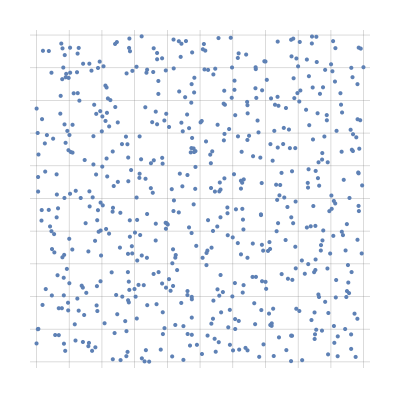

```mathematica
ListPlot[listIter,AspectRatio->Automatic, GridLines->{{-0.2,-0.16,-0.12,-0.08,-0.04,0,0.04,0.08,0.12,0.16,0.2}, {-0.2,-0.16,-0.12,-0.08,-0.04,0,0.04,0.08,0.12,0.16,0.2}}]
```

```mathematica
RingSum[ring_]:=ring*(ring+1)/2
```

```mathematica
Radius[ring_,strata_]:= Sqrt[(RingSum[ring])/strata]
```

```mathematica
(*Generate a line for a stratum*)
```

```mathematica
TwoPointsLine [stratum_,ring_,strata_]:= Block [{x,y,n,m},
angle = stratum*(2*Pi/ring);
x = Cos[angle]*Radius[(ring-1),strata];
y = Sin[angle]*Radius[(ring-1),strata];
n = Cos[angle]*Radius[(ring),strata];
m = Sin[angle]*Radius[(ring),strata];
{{x,y},{n,m}}
]
```

```mathematica
(*Generate separation lines*)
```

```mathematica
LinesGenerator [strata_]:= Block[{stratum,ring,listPointLines},
stratum = 1;
ring = 1;
listPointLines = {};
While[RingSum[ring]<=strata,AppendTo[listPointLines,TwoPointsLine[stratum,ring,strata]];stratum = stratum +1;
stratum = If[stratum>ring,1,stratum];
ring = If[stratum ==1,++ring,ring]
];
Line[listPointLines]
]
```

```mathematica
LinesGenerator[120]
```

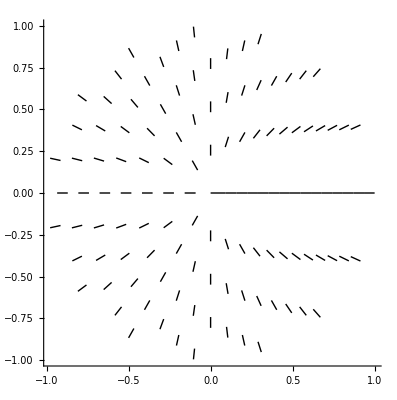

```mathematica
Show[%208,Axes->True]
```

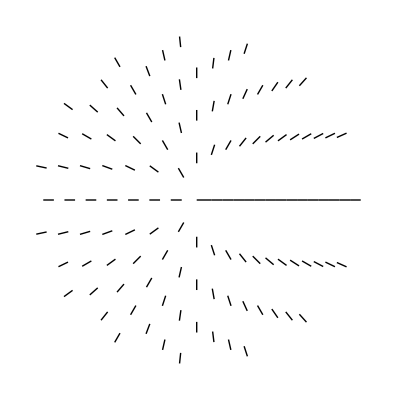

```mathematica
Show[%209,Axes->False]
```

```mathematica
(*Generate the circles*)
```

```mathematica
Circles [maxRing_]:= Block[{circ},
ring = 1;
strata = 120;
circList ={};
While[ring<=maxRing,
circ = Circle[{0,0},Radius[ring,strata]];
AppendTo[circList,circ];
ring++
];
circList
]
```

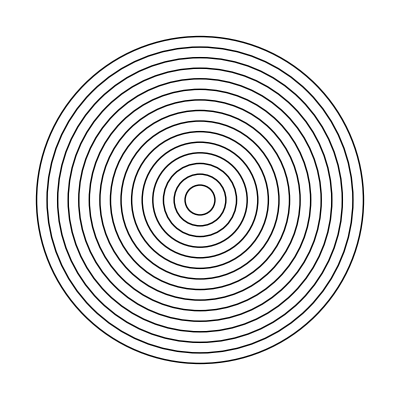

```mathematica
Graphics[Circles[15]]
```

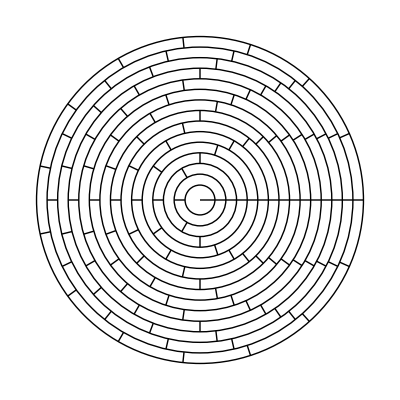

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
(*Disk strategy*)
```

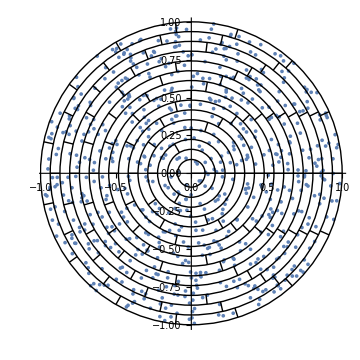

```mathematica
Show[%19,ImageSize->{360,360},AspectRatio->Full]
```

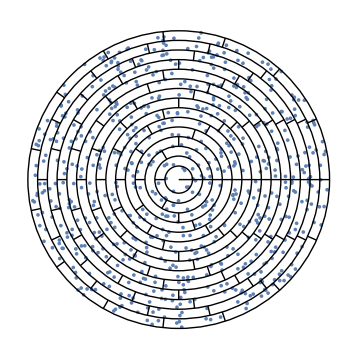

```mathematica
Show[%20,Axes->False]
```

```mathematica
radRing[i_,n_]:= ((√i)/(√n))
```

```mathematica
(*Basic Stratification*)
```

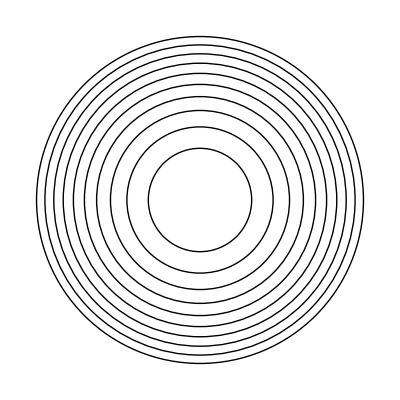

```mathematica
Graphics[Table[Circle[{0,0},radRing[i,10]],{i,10}]]
```

```mathematica
(*2D disk scene generation*)
```

```mathematica
p2[i_,n_]:= Block[{x,y}, 
θ = Random[] 2 Pi;
r =  (((√i)/(√n))^2-((√(i-1))/(√n))^2) Random[]+ ((√(i-1))/(√n))^2;
x=√r Cos[θ];
y = √r Sin[θ];
{x,y}
]
```

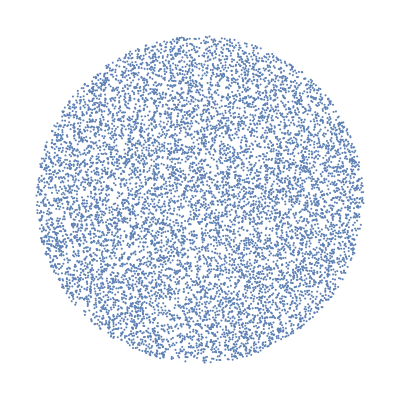

```mathematica
ListPlot[Table[p2[i,10000], {i,10000}],Axes->{False,False},AspectRatio->Automatic]
```

```mathematica
(*Genaration of the scene using spherical coordinates for 10000 photons*)
```

```mathematica
threeDW [i_,n_]:= Block[{x,y,z},
Theta= 2 * Pi * Random[];
Phi=  Random[Real,{-1,1}];
r =(((i^(1/3)/n^(1/3))^3-((i-1)^(1/3)/n^(1/3))^3)*Random[]+((i-1)^(1/3)/n^(1/3))^3)^(1/3);
x =r * Cos[Theta]* √(1-Phi^2);
y = r * Sin[Theta]* √(1-Phi^2);
z = r * Phi;
{x,y,z}
]
```

```mathematica
ListPointPlot3D[Table[threeDW[i,10000], {i,10000}],Axes->{False,False},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
(*Comparing rejection and spherical*)
```

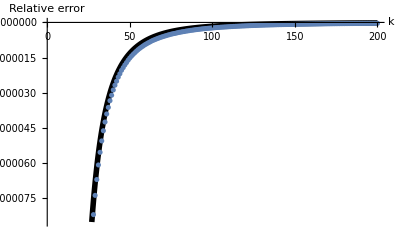

```mathematica
(*3D Silverman 100 Millions*)
```

```mathematica
(*Silverman 2D 50 Millions*)
```